```mathematica
SIntegral=Integrate[-Log[1-n]/n-Log[n]/(1-n),n]
```

-PolyLog[2,1-n]+PolyLog[2,n]

```mathematica
(*
ϵ=βB/2 is the "small" parameter;
z=Exp[βμ] is the fugacity (not necessarily big or small);
*)
Srsv=(SIntegral/.n->1/(Exp[-ϵ]/z+1))-(SIntegral/.n->1/(Exp[ϵ]/z+1));
(*Even terms are zero*)
SrsvϵPwrCoeff=Table[SeriesCoefficient[Srsv,{ϵ,0,ϵpwr}],{ϵpwr,1,5,2}];
```

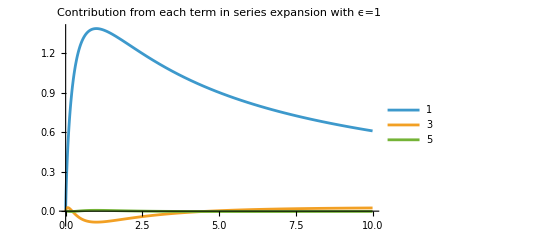

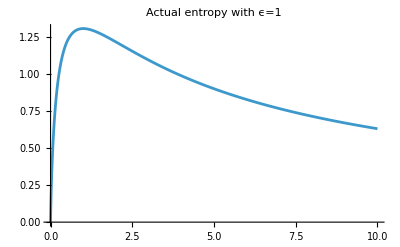

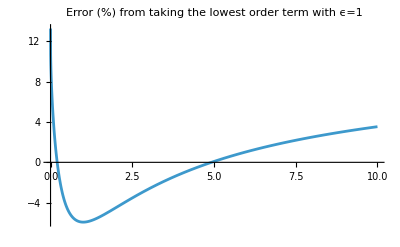

```mathematica
ϵactual=1;(*0.5 when B=kT*)
SrsvAtϵactual=Srsv/.ϵ->ϵactual;
SrsvϵPwrActual=Table[SeriesCoefficient[Srsv,{ϵ,0,ϵpwr}]*ϵ^ϵpwr,{ϵpwr,1,5,2}]/.ϵ->ϵactual;
SrsvϵHigher=SrsvAtϵactual-SrsvϵPwrActual[[1]];
Plot[SrsvϵPwrActual,{z,0,10},PlotLegends->{"1","3","5"},PlotLabel->"Contribution from each term in series expansion with ϵ="<>ToString[ϵactual]]
Plot[SrsvAtϵactual,{z,0,10},PlotLabel->"Actual entropy with ϵ="<>ToString[ϵactual]]
Plot[100*SrsvϵHigher/SrsvAtϵactual,{z,0,10},PlotLabel->"Error (%) from taking the lowest order term with ϵ="<>ToString[ϵactual]]
```